(-26+5 ⅇ^3)/ⅇ^4

1.363191

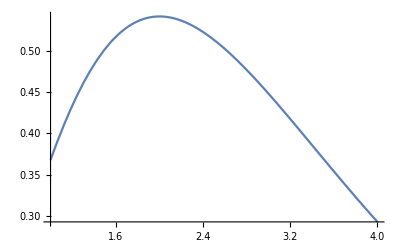

```mathematica
g=x^2 Exp[-x];
A=Integrate[g,{x,1,4}]
N[A,7] (*This provides 7 significant figures*)
Plot[g,{x,1,4}]
```

```mathematica
k=1/A;
f=k*g;
Integrate[f,{x,1,4}]
```

1

```mathematica
EV=Integrate[x*f,{x,1,4}];
EV//N
Var=Integrate[(x-EV)^2f,{x,1,4}];
Var//N
Sqrt[Var]//N
```

2.40997

0.66221

0.813763

Let’s compute the probability P(X<=3)

```mathematica
Integrate[f,{x,1,3}]//N
```

0.728451

Let’s compute the probability P(2<=X<=3)

```mathematica
Integrate[f,{x,2,3}]//N
```

0.371902

```mathematica
g=Sqrt[49-x^2];
A=Integrate[g, {x,0,7}];
f=g/A;
Integrate[f, {x,0,7}];
EV=Integrate[x f, {x,0,7}];
Var=Integrate[(x-EV)^2 f, {x,0,7}];
StDev=Sqrt[Var];
{A,EV,Var,StDev}
{A,EV,Var,StDev}//N
```

{(49 π)/4,28/(3 π),49/4-784/(9 π^2),√(49/4-784/(9 π^2))}

{38.4845,2.97089,3.4238,1.85035}

```mathematica
g=Log[x+1]/x^2;
a=1;
b=5;
A=Integrate[g, {x,a,b}];
f=g/A;
Integrate[f, {x,a,b}];
EV=Integrate[x f, {x,a,b}];
Var=Integrate[(x-EV)^2 f, {x,a,b}];
StDev=Sqrt[Var];
{A,EV,Var,StDev}//N
```

{0.845621,2.27858,1.15167,1.07316}

```mathematica
g=Exp[-3x];
a=0;
b=Infinity;
A=Integrate[g, {x,a,b}];
f=g/A;
Integrate[f, {x,a,b}];
EV=Integrate[x f, {x,a,b}];
Var=Integrate[(x-EV)^2 f, {x,a,b}];
StDev=Sqrt[Var];
{A,EV,Var,StDev}
{A,EV,Var,StDev}//N
```

{1/3,1/3,1/9,1/3}

{0.333333,0.333333,0.111111,0.333333}